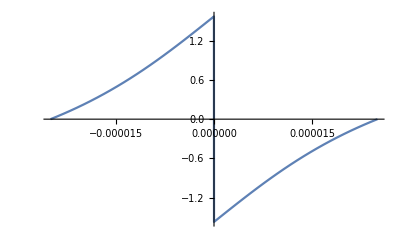

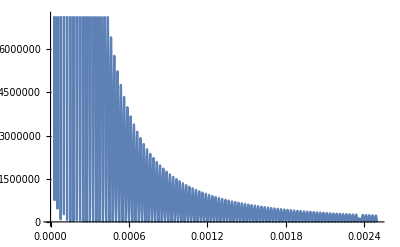

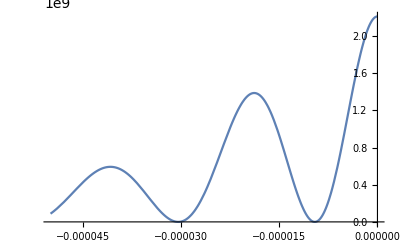

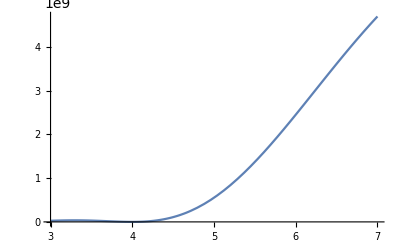

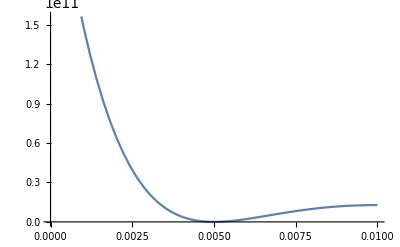

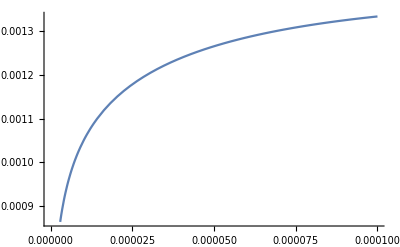

0.0104891

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.0039374

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.00328255

0.0018073

0.00119412

0.000157592

0.00119133

0.00119937

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00124108 and 1.40399×10^-8 for the integral and error estimates.

0.00124108

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.00558682

1.18376703584689×10^5450

NIntegrate::inumr: The integrand 0.000184835\ Sin[theta]\ (ⅇ^π^2/500000000000000000\ lambda^2 + lambda\ Csc[phi]\ Csc[theta]\ (4\ π^2/1599999999\ lambda^2 + 4\ π^2\ « 1 »^2\ « 1 »^2/lambda^2 - 4\ π^2\ « 1 »^2\ Sin[theta]^2/lambda^2)/4\ π\ √4\ π^2/1599999999\ « 6 »^2 + 4\ « 2 »\ « 1 »^2/« 6 »^2\ √1 + lambda^2\ Csc[« 1 »]^2\ « 1 »^2\ Plus[« 3 »]^2/16\ π^2\ Plus[« 2 »])/lambda\ (1/1600000000 + theta^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{3/10000000, 7/10000000}, {0, 6.28319}}.

NIntegrate::inumr: The integrand 0.000184835\ ⅇ^-7.85398×10^-9/lambda\ Sin[theta]\ (ⅇ^π^2/500000000000000000\ lambda^2 - Sin[0.000314159\ theta/lambda - ArcTan[Times[« 7 »]]])/lambda\ (1/1600000000 + theta^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{3/10000000, 7/10000000}, {0, 6.28319}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

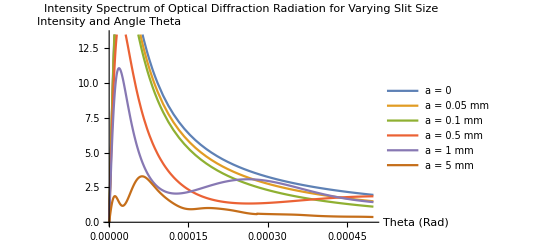

NIntegrate::inumr: The integrand 0.0036485\ ⅇ^-0.001\ √4\ « 1 »/1 « 8 » 9\ « 1 » + « 1 »/« 1 »\ Sin[theta]\ (2\ ⅇ^4\ Power[« 2 »]\ Power[« 2 »]/1599999999 + 4\ « 3 »\ Power[« 2 »]/1250000000 + 2\ Sin[ArcTan[1/4\ lambda\ Power[« 2 »]\ Csc[« 1 »]\ Csc[« 1 »]\ Power[« 2 »]\ Plus[« 3 »]] - 0.00628319\ Sin[phi]\ Sin[theta]/lambda])/lambda^3\ (4\ π^2/1599999999\ lambda^2 + 4\ π^2\ Cos[phi]^2\ Sin[theta]^2/lambda^2 + 4\ π^2\ Sin[phi]^2\ Sin[theta]^2/lambda^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{3/10000000, 7/10000000}, {0, 6.28319}}.

NIntegrate::inumr: The integrand 0.0036485\ ⅇ^-0.001\ « 1 »\ Sin[theta]\ (ⅇ^4\ Power[« 2 »]\ Power[« 2 »]/1599999999 + 4\ « 3 »\ Power[« 2 »]/1250000000\ (ⅇ^-0.0001\ √Plus[« 2 »] + ⅇ^0.0001\ √Plus[« 2 »]) + 2\ Sin[ArcTan[1/4\ lambda\ Power[« 2 »]\ Csc[« 1 »]\ Csc[« 1 »]\ Power[« 2 »]\ Plus[« 3 »]] - 0.00628319\ « 1 »\ Sin[theta]/lambda])/lambda^3\ (4\ π^2/1599999999\ lambda^2 + 4\ π^2\ Cos[phi]^2\ Sin[theta]^2/lambda^2 + 4\ π^2\ Sin[phi]^2\ Sin[theta]^2/lambda^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{3/10000000, 7/10000000}, {0, 6.28319}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

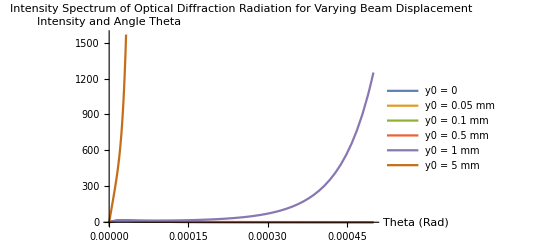

```mathematica
gamma=40000;
eps1=1;
eps2=11.9;
eps3=250;
c=299792458;
hbar=1.05457173*^-34;
beta=Sqrt[1-1/gamma^2];
e=1.602*^-19;
n=2*^10;(*number of electrons*)
q=n*e;(*bunch charge in Coulombs*)
rad=0.02 ;(*lense diameter in m*)
d=0.05 ;(*distance from foil to lens in m*)
a=0.020000000; (*size of diffraction slit in m*)
lowerlambda=300*^-9;(*Visible Spectrum m*)
averagelambda=500*^-9;
upperlambda=700*^-9;
eps0=8.854*^-12;
sigx=20*^-6;
sigy=sigx;
sigz=20*^-6;
alpha=7.297*^-3;

thetalens=ArcTan[a/(2*d)];
thetamax=1/gamma;

k[lambda_]:=
2*Pi/lambda
kx[lambda_,theta_,phi_]:=
k[lambda]*Sin[theta]*Cos[phi]
ky[lambda_,theta_,phi_]:=
k[lambda]*Sin[theta]*Sin[phi]
Eta[lambda_]:=
k[lambda]/(beta*gamma)
f[lambda_,theta_,phi_]:=
Sqrt[kx[lambda,theta,phi]^2+Eta[lambda]^2]

Phi[lambda_,theta_,phi_]:=
ArcTan[(f[lambda,theta,phi]^2-ky[lambda,theta,phi]^2)/(-2*f[lambda,theta,phi]*ky[lambda,theta,phi])]
(*(f[lambda,theta,phi]^2+ky[lambda,theta,phi]^2)/(-2*f[lambda,theta,phi]*ky[lambda,theta,phi])*)

Nsingle[lambda_,theta_,phi_,y_,a_]:=
1/2*alpha/lambda^3*Exp[-a*f[lambda,theta,phi]]/(f[lambda,theta,phi]^2+ky[lambda,theta,phi]^2)*(Exp[2*y*f[lambda,theta,phi]]+Exp[-2*y*f[lambda,theta,phi]]-2*Sin[a*ky[lambda,theta,phi]+Phi[lambda,theta,phi]])

Nbunch[lambda_,theta_,phi_,y0_,a_]:=
1/2*alpha/lambda^3*Exp[-a*f[lambda,theta,phi]]/(f[lambda,theta,phi]^2+ky[lambda,theta,phi]^2)*(Exp[2*f[lambda,theta,phi]^2*sigy^2]*(Exp[2*y0*f[lambda,theta,phi]]+Exp[-2*y0*f[lambda,theta,phi]])-2*Sin[a*ky[lambda,theta,phi]+Phi[lambda,theta,phi]])

NbunchPlane[lambda_,theta_,phi_,a_]:=
alpha/(4*Pi^2)*1/lambda*Exp[-2*Pi*a/(gamma*lambda)]/(theta^2+1/gamma^2)*(Exp[8*Pi^2*sigy^2/(gamma*lambda)^2]-Sin[2*Pi*a*theta/lambda+Phi[lambda,theta,phi]])


(*NIntegrate[Sin[theta]*Nsingle[lambda,theta,phi,0],{theta,0,Pi/2},{phi,0,2*Pi},{lambda,300*^-9,700*^-9}]*)
(*DensityPlot[Nbunch[500*^-9,theta,phi,0],{theta,-Pi/2,Pi/2},{phi,0,2*Pi}]*)
(*Plot[2*Pi*Nsingle[500*^-9,0,theta,0],{theta,0,2*Pi}]*)
Plot[Phi[500*^-9,theta,Pi/2],{theta,-1/gamma,1/gamma}]
Plot[{Nbunch[500*^-9,theta,Pi/2,0,a],NbunchPlane[500*^-9,theta,Pi/2]},{theta,0,100/gamma}]
Plot[Nbunch[500*^-9,theta,-Pi/2,0,a],{theta,-2/gamma,0}]
(*Plot[NIntegrate[NbunchPlane[lambda,theta,Pi/2],{lambda,lowerlambda,upperlambda}],{theta,0,Pi/2}]*)
Plot[NbunchPlane[lambda,1/gamma,Pi/2,a],{lambda,lowerlambda,upperlambda}]
Plot[NbunchPlane[500*^-9,1/gamma,Pi/2,a],{a,0,0.01}]
Plot[NIntegrate[Sin[theta]*NbunchPlane[lambda,theta,Pi/2,a],{lambda,lowerlambda,upperlambda},{theta,0,Pi/2},MaxRecursion->12],{a,0,0.0001}]
(*NIntegrate[Sin[theta]*NbunchPlane[lambda,theta,Pi/2,a],{lambda,lowerlambda,upperlambda},{theta,0,Pi/2},MaxRecursion->12]*)

NIntegrate[Sin[theta]*Nsingle[averagelambda,theta,phi,0,0],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},{theta,0,Pi/2},MaxRecursion->12]
NIntegrate[Sin[theta]*Nsingle[averagelambda,theta,phi,0,0.00005],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},{theta,0,Pi/2},MaxRecursion->12]
NIntegrate[Sin[theta]*Nsingle[averagelambda,theta,phi,0,0.0001],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},{theta,0,Pi/2},MaxRecursion->12]
NIntegrate[Sin[theta]*Nsingle[averagelambda,theta,phi,0,0.0005],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},{theta,0,Pi/2},MaxRecursion->12]
NIntegrate[Sin[theta]*Nsingle[averagelambda,theta,phi,0,0.001],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},{theta,0,Pi/2},MaxRecursion->12]
NIntegrate[Sin[theta]*Nsingle[averagelambda,theta,phi,0,0.005],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},{theta,0,Pi/2},MaxRecursion->12]

NIntegrate[Sin[theta]*Nsingle[averagelambda,theta,phi,0.00001,0.001],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},{theta,0,Pi/2},MaxRecursion->12]
NIntegrate[Sin[theta]*Nsingle[averagelambda,theta,phi,0.00005,0.001],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},{theta,0,Pi/2},MaxRecursion->12]
NIntegrate[Sin[theta]*Nsingle[averagelambda,theta,phi,0.0001,0.001],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},{theta,0,Pi/2},MaxRecursion->12]
NIntegrate[Sin[theta]*Nsingle[averagelambda,theta,phi,0.0005,0.001],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},{theta,0,Pi/2},MaxRecursion->12]
NIntegrate[Sin[theta]*Nsingle[averagelambda,theta,phi,0.001,0.001],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},{theta,0,Pi/2},MaxRecursion->12]

Plot[{NIntegrate[Sin[theta]*NbunchPlane[lambda,theta,phi,0],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},MaxRecursion->12],NIntegrate[Sin[theta]*NbunchPlane[lambda,theta,phi,0.00005],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},MaxRecursion->12],NIntegrate[Sin[theta]*NbunchPlane[lambda,theta,phi,0.0001],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},MaxRecursion->12],NIntegrate[Sin[theta]*NbunchPlane[lambda,theta,phi,0.0005],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},MaxRecursion->12],NIntegrate[Sin[theta]*NbunchPlane[lambda,theta,phi,0.001],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},MaxRecursion->12],NIntegrate[Sin[theta]*NbunchPlane[lambda,theta,phi,0.005],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},MaxRecursion->12]},{theta,0,20/gamma},AxesLabel-> {"Theta (Rad)","Intensity and Angle Theta"},PlotLabel->"Intensity Spectrum of Optical Diffraction Radiation for Varying Slit Size",PlotLegends->{"a = 0","a = 0.05 mm","a = 0.1 mm","a = 0.5 mm","a = 1 mm","a = 5 mm"}]

Plot[{NIntegrate[Sin[theta]*Nbunch[lambda,theta,phi,0,0.001],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},MaxRecursion->12],NIntegrate[Sin[theta]*Nbunch[lambda,theta,phi,0.00005,0.001],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},MaxRecursion->12],NIntegrate[Sin[theta]*Nbunch[lambda,theta,phi,0.0001,0.001],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},MaxRecursion->12],NIntegrate[Sin[theta]*Nbunch[lambda,theta,phi,0.0005,0.001],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},MaxRecursion->12],NIntegrate[Sin[theta]*Nbunch[lambda,theta,phi,0.001,0.001],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},MaxRecursion->12],NIntegrate[Sin[theta]*Nbunch[lambda,theta,phi,0.005,0.001],{lambda,lowerlambda,upperlambda},{phi,0,2*Pi},MaxRecursion->12]},{theta,0,20/gamma},AxesLabel-> {"Theta (Rad)","Intensity and Angle Theta"},PlotLabel->"Intensity Spectrum of Optical Diffraction Radiation for Varying Beam Displacement",PlotLegends->{"y0 = 0","y0 = 0.05 mm","y0 = 0.1 mm","y0 = 0.5 mm","y0 = 1 mm","y0 = 5 mm"}]
```